# Linkage map construction in multiparental populations

## Chaozhi Zheng Wageningen University and Research 30 August 2018

## Outlines

Selection mapping population

Simulate genomic data

Map construction

Compare with true map

## Load MagicMap

First set directory to the directory of the Mathematica packages.
Then load the package by functions Needs or Get. 
Use  the directory of the current notebook as the work directory.

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]];
Get["MagicMap`"]
myParallelNeeds["MagicMap`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\StatisticalPackages\RABBIT Software\RABBIT_Tutorial

Get help information on functions or options by ?

```mathematica
?"MagicMap`*"
?graphLaplacian
```

graphLaplacian is an option to specify one of three graph Laplacians: "unNormalized","rwNormalized",or "symNormalized".

## Select an example population

```mathematica
codels={"f2","2wayril-self6","cp","4wayril-self4"}; popcode=codels[[1]];
pedls=Table[pedigree=compilePopPedigree[codels[[i]]];
Column[{"popcode = "<>codels[[i]],pedigreePlot[pedigree,ImageSize->Switch[i,1|2,100,_,200]]}],{i,Length[codels]}];
TabView[Transpose[{codels,Thread[{"F2","2-way RIL","CP","4-way RIL"}->pedls]}],Dynamic[popcode],ImageSize->Automatic]
```

f22wayril-self6cp4wayril-self4

## Simulate genomic data

```mathematica
popsize=100; Print["population code = ", popcode];
simpedinforfile=simPedigreeInfor[popcode,sampleSize->popsize,outputFileID->"Example"];
isfounderinbred=popcode=!="cp";
datafiles=magicGeneDropping["Arabidopsis_MAGIC_19FounderHaplo.csv",simpedinforfile,dropMonomorphic->True,outputFileID->"Example",isFounderInbred->isfounderinbred,founderGenotypeMissing->0.1,offspringGenotypeMissing->0.1,offspringAllelicError->0.05,isPrintTimeElapsed->True];
```

population code = f2

magicGeneDropping. Start date = Thu 25 Apr 2019 09:56:55

Time elapsed = 0. Seconds. 	Start simulating offspring genomes in terms of FGL lists.

Time elapsed = 1. Seconds. 	Start dropping founder alleles on the offspring FGL lists.

Time elapsed = 1.5 Seconds. 	Start simulating allelic errors in founders and offspring.

The realized fraction of missing genotypes in founders: 0.089

The realized fraction of missing genotypes in offspring: 0.099

Saving true values and simulated data. Thu 25 Apr 2019 09:56:57
	True FGL | Example_TrueValues_Fgl.txt
True FGL diplotype | Example_TrueValues_FglDiplotype.csv
True diplotype | Example_TrueValues_Diplotype.csv
Observed genotype | Example_ObservedGenotype.csv

Done! Finished date =Thu 25 Apr 2019 09:56:57. 	Time elapsed = 2.1 Seconds.

## Map construction

```mathematica
Options[magicMap]
```

{outputFileID→,isPrintTimeElapsed→True,isRunInParallel→True,founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,computingLodType→both,sequenceDataOption→{isFounderAllelicDepth→Automatic,isOffspringAllelicDepth→Automatic,minPhredQualScore→30,priorFounderCallThreshold→0.99},minLodSaving→1,miniComponentSize→5,graphLaplacian→rwNormalized,eigenVectorSelection→eigenratio,nConnectedComponent→1,lodTypeClustering→both,lodTypeOrdering→both,minLodClustering→Automatic,minLodOrdering→Automatic,nNeighborFunction→(√#1&),nNeighborSaving→10,referenceMap→None,delStrongCrossLink→True,minLodSegregateBin→∞,isImputingFounder→True,detectingThreshold→Automatic,imputingThreshold→1,nReplicateAnnealing→1,initTemperature→2,coolingRatio→0.85,freezingTemperature→0.5,deltLoglThreshold→1,maxFreezeIteration→15,dupebinMarker→True,redoSimilarity→True}

Example_ObservedGenotype.csv

-----------------------------------------------------Binning Markers----------------------------------------------------------------

magicsnpBinning. Start date = Thu 25 Apr 2019 09:56:58. Outputfiles = {Example_dupebin_magicsnp.csv,Example_dupebin_binning.csv,Example_dupebin_adjacencymatrix.txt}

#SNPs = 387; #Bins = 387

Done. Finished date = Thu 25 Apr 2019 09:57:00. Time elapsed in magicsnpBinning= 2.18 seconds.

--------------------------------------------------Calculate PairwiseFraction----------------------------------------------------------

magicPairwiseSimilarity. Start date = Thu 25 Apr 2019 09:57:00. Outputfile = Example_pairwise_similarity.txt

{#founder, #offspring, #SNP} ={2,100,387}

Done! Finished date =Thu 25 Apr 2019 09:57:27. 	Time elapsed in magicPairwiseSimilarity = 27. Seconds.

-----------------------------------------------------Construct LinkageMap-------------------------------------------------------------

magicMapConstruct. Start date = Thu 25 Apr 2019 09:57:27. Output map file = Example_pairwise_linkagemap.csv

Size of 1 connected componets: {387}; dropping components with size <= 5!

The option value of minLodClustering is set to 2.!

Size of 5 groups = {98,68,76,63,82} and #ungrouped markers = 0 after spectral clustering!Time elapsed = 3.6 Seconds.

The option value of minLodOrdering is set to {2., 2., 2., 2., 2.}!

# NearestNeighbors = {10,9,9,9,10}

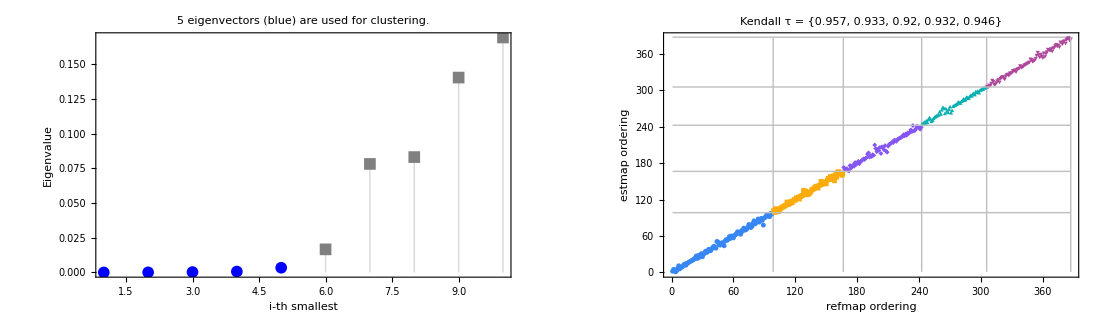

Done! Finished date =Thu 25 Apr 2019 09:57:32. 	Time elapsed in magicMapConstruct = 5.2 Seconds.

-------------------------------------------------------Refine LinkageMap-------------------------------------------------------------

magicMapRefine. Start date = Thu 25 Apr 2019 09:57:32. Outputfiles = {Example_refine_linkagemap.csv,Example_refine_history.txt}

detectingThreshold is set to 0.9 for indepModel

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={1,2,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={4,1.22825,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={7,0.754299,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={11,0.284484,True,True,False}

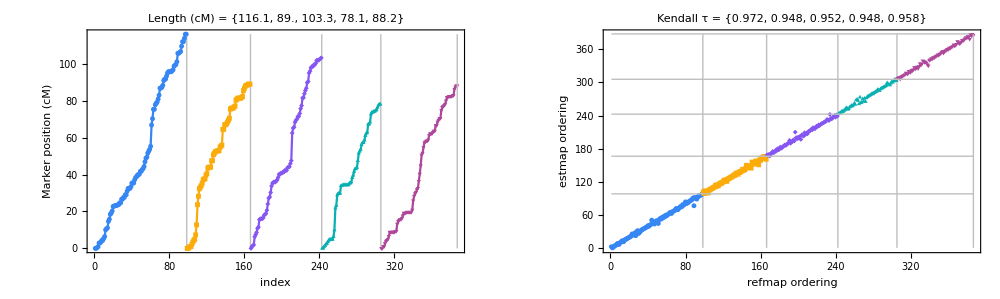

# iterations = {{15},{15},{15},{15},{15}}

Done! Finished date =Thu 25 Apr 2019 10:03:13. 	Time elapsed in magicMapRefine = 340. Seconds.

--------------------------------------------------------Export finalMap--------------------------------------------------------------

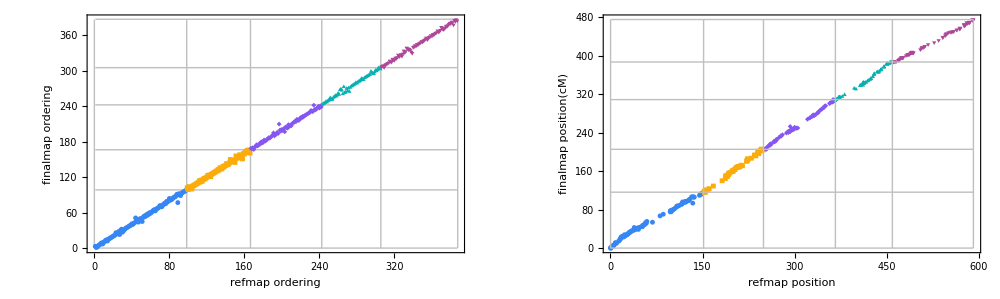

Done. Finished date = Thu 25 Apr 2019 10:03:13.	Time elapsed in all steps of magicMap = 375.07 seconds.

------------------------------------------------------------End---------------------------------------------------------------------

```mathematica
genodatafile=Last[datafiles]
Export[truemapfile="Example_TrueMap.csv",Transpose[Import[datafiles[[3]],Path->Directory[]][[2;;4]]]];
model=Switch[popcode,"f2","indepModel","cp","jointModel", _,"depModel"];
ngroup=5;
outputfiles=magicMap[genodatafile,model,simpedinforfile,ngroup,isFounderInbred->isfounderinbred,referenceMap->truemapfile,outputFileID->"Example"];
```

## Compare with true map

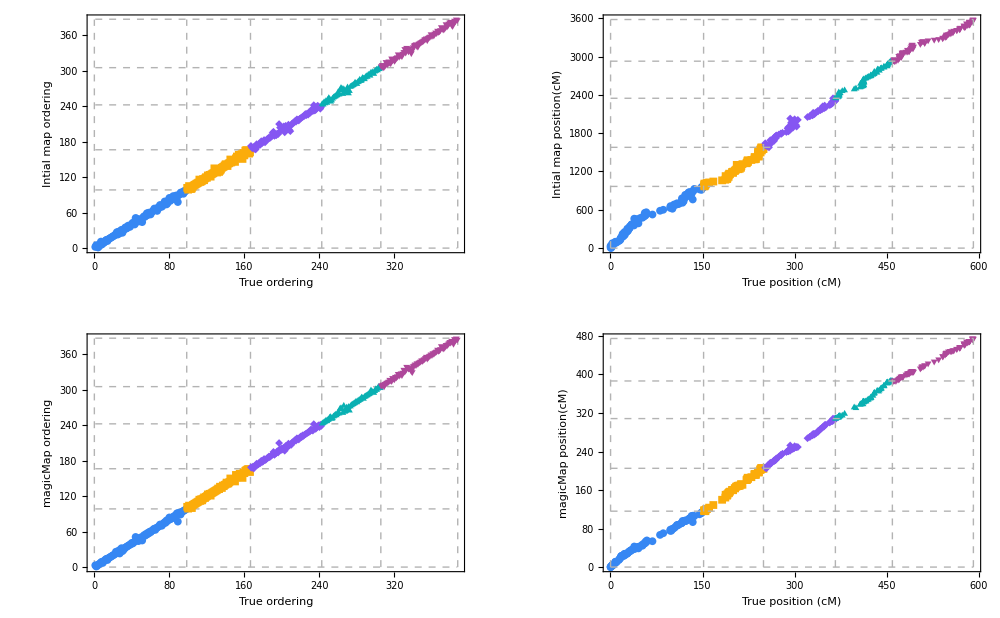

```mathematica
initmapfile="Example_pairwise_linkagemap.csv"; refinemapfile="Example_finalmap.csv";
xylabel={{{"True ordering","Intial map ordering"},{"True position (cM)","Intial map position(cM)"}},{{"True ordering","magicMap ordering"},{"True position (cM)","magicMap position(cM)"}}};
gg=Table[plotMapComparison[truemapfile,file,#,Directive[Dashed,Thin,GrayLevel[0.7]],PlotMarkers->{Automatic,8}]&/@{True,False},{file,{initmapfile,refinemapfile}}];
gg=MapThread[Show[#1,Frame->True,LabelStyle->Directive[FontSize->20,Black],FrameLabel->#2]&,{gg,xylabel},2];
GraphicsGrid[gg,ImageSize->1000]
```

## Visualize heat map

```mathematica
plotHeatMapGUI["Example_pairwise_similarity.txt","Example_finalmap.csv"]
```

## Refereces

Zheng, C., Boer, M. P., and Eeuwijk, F. A. 2018.  Construction of genetic linkage maps in multiparental populations. Submitted.